## TemplateRandomSquareGrid-example.nb

Example Cellzilla2D notebook.

GPL License applies. 
See http://xlr8r.info and http://cellzilla.info for further details.

```mathematica
<<Cellzilla2D.m
```

Cellzilla2D (3.0.51h (15 June 2017)) loaded Sun 18 Jun 2017 08:57:10
using xCellerator 0.95 and XSSA 1.3.2
GPL License Terms Apply

There are 116 cells in the tissue.

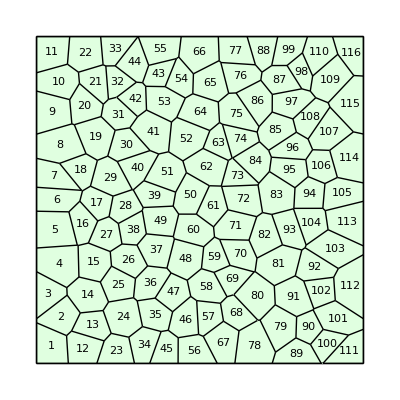

```mathematica
q=TemplateRandomSquareGrid[110, {-50, -50}, {50, 50}];
Print["There are ", NTissueCells[q], " cells in the tissue."];  
ShowTissue[q, "CellNumbers"-> True]
```